## 1 Import all independent variables datasets

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]];
```

### SBP price

```mathematica
prices01to24=Import["exp_prices01to24.csv"];
prices01to24DS=Dataset[AssociationThread[prices01to24[[1]]->ToExpression[#]]&/@prices01to24[[2;;]]];
dailyAvgSBP01to24=Query[GroupBy["SETTLEMENT_DATE"], Mean, "SBP"][prices01to24DS];
dailyAvgSBP01to24TS=TimeSeries[dailyAvgSBP01to24//Normal];
trendSBP01to24TS=MeanFilter[dailyAvgSBP01to24TS,Quantity[12,"Months"]]
```

TimeSeries[…]

### Fuel types

```mathematica
fuel09to24=Import["exp_fuel09to24.csv"];
fuel09to24DS=Dataset[AssociationThread[fuel09to24[[1]]->ToExpression[#]]&/@fuel09to24[[2;;]]];
dailyAvgRenPerc09to23=Query[GroupBy["SETTLEMENT_DATE"], Mean, "RENEWABLE_perc"][fuel09to24DS];
dailyAvgRenPerc09to23TS=TimeSeries[dailyAvgRenPerc09to23//Normal];
trendRenPerc09to23TS=MeanFilter[dailyAvgRenPerc09to23TS,Quantity[12,"Months"]]
```

TimeSeries[…]

### Temperature

```mathematica
avgTemp09to22=Import["exp_temp09to22.csv"];
avgTemp09to22TS=TimeSeries[ToExpression[#]&/@avgTemp09to22];
trendTemp09to22=MeanFilter[avgTemp09to22TS,Quantity[12,"Months"]]
```

TimeSeries[…]

### Real GDP

```mathematica
realGDP=Import["exp_realGDP93to22.csv"];
realGDPTS=TimeSeries[ToExpression[#]&/@realGDP]
```

TimeSeries[…]

### Population

```mathematica
populationTS=Differences[CountryData["UK",{{"Population"},{2008,2023}}]]
```

TimeSeries[…]

### Gas demand

```mathematica
gas=Import["exp_gas98to23.csv"];
gasTS=TimeSeries[ToExpression[#]&/@gas]
```

TimeSeries[…]

### Electricity consumer price

```mathematica
consumerPrice=Import["exp_consumerPrice70to22.csv"];
consumerPriceTS=TimeSeries[ToExpression[#]&/@consumerPrice]
```

TimeSeries[…]

### New builds

```mathematica
build=Import["exp_newBuild09to22.csv"];
buildTS=TimeSeries[ToExpression[#]&/@build]
```

TimeSeries[…]

### EPC rating

```mathematica
efficiency=Import["exp_EPC13to23.csv"];
efficiencyTS=TimeSeries[ToExpression[#]&/@efficiency]
```

TimeSeries[…]

```mathematica
RegularlySampledQ[efficiencyTS]
```

True

## 2 Import electricity demand dataset

```mathematica
monthlyTotalDemand09to23=Import["exp_monthly_total_demand09to23.csv"];
```

```mathematica
monthlyTotalDemand09to23TS=TimeSeries[ToExpression[#]&/@monthlyTotalDemand09to23];
```

```mathematica
trend09to23TS=MeanFilter[monthlyTotalDemand09to23TS,Quantity[12,"Months"]];
```

## 3 Resample all datasets at the same time points

```mathematica
refTimes=efficiencyTS["Times"];
```

```mathematica
demand=TimeSeriesResample[trend09to23TS,{refTimes}]["Values"];
```

```mathematica
SBP=TimeSeriesResample[dailyAvgSBP01to24TS,{refTimes}]["Values"];
renewables=TimeSeriesResample[dailyAvgRenPerc09to23TS,{refTimes}]["Values"];
temperature=TimeSeriesResample[trendTemp09to22,{refTimes}]["Values"];
GDP=TimeSeriesResample[realGDPTS,{refTimes}]["Values"];
population=TimeSeriesResample[populationTS,{refTimes}]["Values"];
energyEfficiency=TimeSeriesResample[efficiencyTS,{refTimes}]["Values"];
newBuild=TimeSeriesResample[Accumulate[buildTS],{refTimes}]["Values"];
gasDemand=TimeSeriesResample[gasTS,{refTimes}]["Values"];
consumer=TimeSeriesResample[ consumerPriceTS,{refTimes}]["Values"][[All,1]];
```

```mathematica
features=Transpose[{SBP,consumer,renewables,temperature,GDP,population,gasDemand,newBuild,energyEfficiency}];
```

```mathematica
features//Dimensions
```

{11,9}

```mathematica
featuresName={"Bid price","Electricity CPI","Percentage renewables","Average temperature","Real GDP","Population growth","Gas demand","Number new builds","Housing efficiency"}
```

{Bid price,Electricity CPI,Percentage renewables,Average temperature,Real GDP,Population growth,Gas demand,Number new builds,Housing efficiency}

## 4 Correlation matrix

### 4.1 Correlation between features

```mathematica
HeatMap[values0_,names0_,vfeatures0_]:=Module[
{values=values0,names=names0,vf=vfeatures0,table1,table2,table3},

table1=Table[If[i==j,
1,
If[i<j,
Style[#,
ColorData["DarkRainbow"][Abs[#]],
If[SpearmanRankTest[features[[All,i]],features[[All,j]],"PValue"]<0.05,Underlined,FontWeight->Plain]
]&@SpearmanRankTest[features[[All,i]],features[[All,j]],"TestStatistic"]],
{}],
{i,vf},{j,vf}];
table2=Prepend[table1,names];
Grid[Append[Transpose[table2],Join[{""},names]],
ItemSize->12,
Dividers->{{2->Black},{-2->Black}},
Spacings->{0,0.2}]

]
```

```mathematica
HeatMap[features[[All,All]],featuresName[[{3,4,5,6,8}]],{3,4,5,6,8}]
```

Percentage renewables | 1 |  |  |  | 
Average temperature | 0.845455 | 1 |  |  | 
Real GDP | 0.890909 | 0.681818 | 1 |  | 
Population growth | -0.890909 | -0.745455 | -0.745455 | 1 | 
Number new builds | 0.954545 | 0.809091 | 0.809091 | -0.936364 | 1
 | Percentage renewables | Average temperature | Real GDP | Population growth | Number new builds

```mathematica
tableA1=HeatMap[features[[All,All]],featuresName,{1,2,3,4,5,6,7,8,9}]
```

Bid price | 1 |  |  |  |  |  |  |  | 
Electricity CPI | -0.554545 | 1 |  |  |  |  |  |  | 
Percentage renewables | -0.481818 | 0.945455 | 1 |  |  |  |  |  | 
Average temperature | -0.527273 | 0.809091 | 0.845455 | 1 |  |  |  |  | 
Real GDP | -0.572727 | 0.827273 | 0.890909 | 0.681818 | 1 |  |  |  | 
Population growth | 0.554545 | -0.890909 | -0.890909 | -0.745455 | -0.745455 | 1 |  |  | 
Gas demand | 0.545455 | -0.6 | -0.463636 | -0.654545 | -0.427273 | 0.518182 | 1 |  | 
Number new builds | -0.6 | 0.954545 | 0.954545 | 0.809091 | 0.809091 | -0.936364 | -0.563636 | 1 | 
Housing efficiency | -0.252436 | 0.640439 | 0.649788 | 0.388003 | 0.490847 | -0.827428 | -0.158941 | 0.715234 | 1
 | Bid price | Electricity CPI | Percentage renewables | Average temperature | Real GDP | Population growth | Gas demand | Number new builds | Housing efficiency

```mathematica
Export["TableA1.jpeg",tableA1]
```

TableA1.jpeg

```mathematica
correlationMatrix[values0_,names0_,vfeatures0_]:=Module[
{values=values0,names=names0,vf=vfeatures0,table1,table2,table3},

table1=Table[If[i==j,
1,
SpearmanRankTest[features[[All,i]],features[[All,j]],"TestStatistic"]],
{i,vf},{j,vf}];
table2=Prepend[table1,names];
Prepend[Transpose[table2],Join[{""},names]]
]
```

We want to find a threshold to separate significant variables from others. By performing a cluster analysis on the values of the correlation coefficients we find that a value of 0.7 is the threshold between the two clusters.

```mathematica
Sort[#]&/@FindClusters[Select[Flatten[Abs[correlationMatrix[features[[All,All]],featuresName,{1,2,3,4,5,6,7,8,9}][[2;;,2;;]]]],#<1.&],2]
```

{{0.715234,0.715234,0.745455,0.745455,0.745455,0.745455,0.809091,0.809091,0.809091,0.809091,0.809091,0.809091,0.827273,0.827273,0.827428,0.827428,0.845455,0.845455,0.890909,0.890909,0.890909,0.890909,0.890909,0.890909,0.936364,0.936364,0.945455,0.945455,0.954545,0.954545,0.954545,0.954545},{0.158941,0.158941,0.252436,0.252436,0.388003,0.388003,0.427273,0.427273,0.463636,0.463636,0.481818,0.481818,0.490847,0.490847,0.518182,0.518182,0.527273,0.527273,0.545455,0.545455,0.554545,0.554545,0.554545,0.554545,0.563636,0.563636,0.572727,0.572727,0.6,0.6,0.6,0.6,0.640439,0.640439,0.649788,0.649788,0.654545,0.654545,0.681818,0.681818}}

We then study the connectivity of these significant variables .

```mathematica
labels={1-> "Bid price",2-> "Electricity CPI",3->"Percentage renewables",4-> "Average temperature",5-> "Real GDP",6->"Population growth",7->"Gas demand",8->"Number new builds",9->"Housing efficiency"};
```

```mathematica
UnitStep[correlationMatrix[features[[All,All]],featuresName,{1,2,3,4,5,6,7,8,9}][[2;;,2;;]]-0.7]
```

{{1,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,1,0},{0,1,1,1,1,0,0,1,0},{0,1,1,1,0,0,0,1,0},{0,1,1,0,1,0,0,1,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,1,1,1,1,0,0,1,1},{0,0,0,0,0,0,0,1,1}}

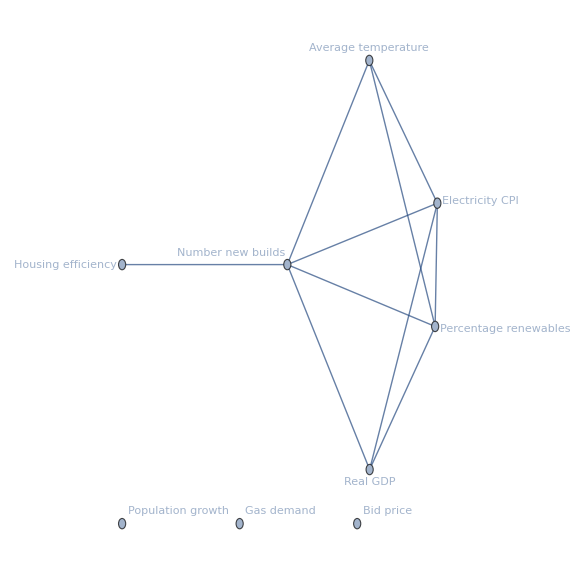

```mathematica
returnsGraph=WeightedAdjacencyGraph[Round[correlationMatrix[features[[All,All]],featuresName,{1,2,3,4,5,6,7,8,9}][[2;;,2;;]] UnitStep[correlationMatrix[features[[All,All]],featuresName,{1,2,3,4,5,6,7,8,9}][[2;;,2;;]]-0.7] ,.01]/. {1.->Infinity,0.->Infinity},VertexLabels->labels,ImageSize->Large,
GraphLayout->"SpringEmbedding"]
```

```mathematica
Export["Figure4.jpeg",returnsGraph]
```

Figure4.jpeg

```mathematica
c=FindGraphCommunities[returnsGraph]
```

{{2,3,4,5},{8,9},{1},{6},{7}}

```mathematica
Values[labels][[#]]&/@c
```

{{Electricity CPI,Percentage renewables,Average temperature,Real GDP},{Number new builds,Housing efficiency},{Bid price},{Population growth},{Gas demand}}

### 4.2 Correlation with energy demand

```mathematica
vf={1,2,3,4,5,6,7,8,9};
table1=Table[
Style[#,
ColorData["DarkRainbow"][Abs[#]],
If[SpearmanRankTest[features[[All,i]],demand,"PValue"]<0.05,Underlined,FontWeight->Plain]
]&@SpearmanRankTest[features[[All,i]],demand,"TestStatistic"],
{i,vf}];
table2=Join[{"Signal's trend"},table1];
table3=Prepend[{Transpose[table2]},Join[{""},featuresName]]//Transpose//Grid
```

| Signal's trend
Bid price | 0.609091
Electricity CPI | -0.945455
Percentage renewables | -0.945455
Average temperature | -0.827273
Real GDP | -0.8
Population growth | 0.918182
Gas demand | 0.572727
Number new builds | -0.990909
Housing efficiency | -0.715234

```mathematica
Export["Table3.jpeg",table3]
```

Table3.jpeg